```mathematica
g=Plot3D[{Legended[√((0.00375 Cos[φ]^2)/A^2-0.005 Cos[φ]^4+(0.00125 Sin[φ]^2)/A^2-0.00375 Sin[2 φ]^2),"Error Plot"]},{A,0,1},{φ,-Pi,Pi},AxesLabel->{A,φ,dφ}]
```

-Graphics3D-

```mathematica
Allerror=(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)

```mathematica
TrigToExp[Allerror]
```

(√(-(-1/4 (-1+B) B (ⅇ^(-ⅈ φ)-ⅇ^(ⅈ φ))^2+1/16 A^2 (ⅇ^(-ⅈ φ)+ⅇ^(ⅈ φ))^4+1/4 (ⅇ^(-ⅈ φ)+ⅇ^(ⅈ φ))^2 (3 (-1+B) B+2 ⅈ A (-1+2 B) (ⅇ^(-ⅈ φ)-ⅇ^(ⅈ φ))-3/4 A^2 (ⅇ^(-ⅈ φ)-ⅇ^(ⅈ φ))^2))/A^2))/(10 √2)

```mathematica
A=0.2;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.353553 √(-0.04 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.12 Sin[φ]^2))

```mathematica
Simplify[0.35355339059327373 √(-0.04000000000000001 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.12000000000000002 Sin[φ]^2))]
```

0.353553 √(-0.04 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.12 Sin[φ]^2))

```mathematica
g1=Plot[{0.35355339059327373 √(-0.04000000000000001 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.12000000000000002 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.2, B=0.5",Smaller]];
```

```mathematica
A=0.3;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.235702 √(-0.09 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.27 Sin[φ]^2))

```mathematica
Simplify[0.23570226039551584 √(-0.09 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.27 Sin[φ]^2))]
```

0.235702 √(-0.09 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.27 Sin[φ]^2))

```mathematica
g2=Plot[{0.23570226039551584 √(-0.09 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.27 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.3, B=0.5",Smaller]];
```

```mathematica
A=0.4;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.176777 √(-0.16 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.48 Sin[φ]^2))

```mathematica
Simplify[0.17677669529663687 √(-0.16000000000000003 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.4800000000000001 Sin[φ]^2))]
```

0.176777 √(-0.16 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.48 Sin[φ]^2))

```mathematica
g3=Plot[{0.17677669529663687 √(-0.16000000000000003 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.4800000000000001 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.4, B=0.5",Smaller]];
```

```mathematica
A=0.5;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.141421 √(-0.25 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.75 Sin[φ]^2))

```mathematica
Simplify[0.1414213562373095 √(-0.25 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+0.75 Sin[φ]^2))]
```

0.141421 √(0.5 Cos[φ]^4+0.25 Sin[φ]^2)

```mathematica
g4=Plot[{0.1414213562373095 √(0.4999999999999999 Cos[φ]^4+0.25 Sin[φ]^2)}, {φ, -Pi, Pi},PlotLegends->Style["A=0.5, B=0.5",Smaller]];
```

```mathematica
A=0.6;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.117851 √(-0.36 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.08 Sin[φ]^2))

```mathematica
g5=Plot[{0.11785113019775792 √(-0.36 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.08 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.6, B=0.5",Smaller]];
```

```mathematica
A=0.7;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.101015 √(-0.49 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.47 Sin[φ]^2))

```mathematica
g6=Plot[{0.10101525445522108 √(-0.48999999999999994 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.4699999999999998 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.7, B=0.5",Smaller]];
```

```mathematica
A=0.8;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.0883883 √(-0.64 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.92 Sin[φ]^2))

```mathematica
g7=Plot[{0.08838834764831843 √(-0.6400000000000001 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.9200000000000004 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.8, B=0.5",Smaller]];
```

```mathematica
A=0.9;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

0.0785674 √(-0.81 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+2.43 Sin[φ]^2))

```mathematica
g8=Plot[{0.07856742013183861 √(-0.81 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+2.43 Sin[φ]^2))}, {φ, -Pi, Pi},PlotLegends->Style["A=0.9, B=0.5",Smaller]];
```

```mathematica
A=1.0;B=0.5;
```

```mathematica
(√(-(A^2 Cos[φ]^4+(-1+B) B Sin[φ]^2+Cos[φ]^2 (3 (-1+B) B+4 A (-1+2 B) Sin[φ]+3 A^2 Sin[φ]^2))/A^2))/(10 √2)
```

(√(-1. (1. Cos[φ]^4-0.25 Sin[φ]^2+Cos[φ]^2 (-0.75+3. Sin[φ]^2))))/(10 √2)

```mathematica
g9=Plot[{(√(-1. (1. Cos[φ]^4-0.25 Sin[φ]^2+Cos[φ]^2 (-0.75+3. Sin[φ]^2))))/(10 √2)}, {φ, -Pi, Pi},PlotLegends->Style["A=1.0, B=0.5",Smaller]];
```

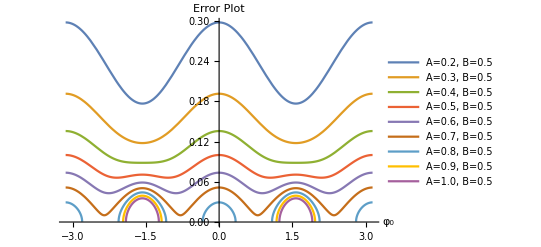

```mathematica
tempcheck1=Plot[{0.35355339059327373 √(-0.04000000000000001 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.12000000000000002 Sin[φ]^2)),0.23570226039551584 √(-0.09 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.27 Sin[φ]^2)),0.17677669529663687 √(-0.16000000000000003 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.4800000000000001 Sin[φ]^2)),0.1414213562373095 √(0.4999999999999999 Cos[φ]^4+0.25 Sin[φ]^2),0.11785113019775792 √(-0.36 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.08 Sin[φ]^2)),0.10101525445522108 √(-0.48999999999999994 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.4699999999999998 Sin[φ]^2)),0.08838834764831843 √(-0.6400000000000001 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+1.9200000000000004 Sin[φ]^2)),0.07856742013183861 √(-0.81 Cos[φ]^4+0.25 Sin[φ]^2-Cos[φ]^2 (-0.75+2.43 Sin[φ]^2)),(√(-1. (1. Cos[φ]^4-0.25 Sin[φ]^2+Cos[φ]^2 (-0.75+3. Sin[φ]^2))))/(10 √2)}, {φ, -Pi, Pi},AxesLabel->{Subscript[φ, 0],Style["Error Plot",FontWeight->Bold,Larger]},PlotLegends->{Style["A=0.2, B=0.5",Smaller],Style["A=0.3, B=0.5",Smaller],Style["A=0.4, B=0.5",Smaller],Style["A=0.5, B=0.5",Smaller],Style["A=0.6, B=0.5",Smaller],Style["A=0.7, B=0.5",Smaller],Style["A=0.8, B=0.5",Smaller],Style["A=0.9, B=0.5",Smaller],Style["A=1.0, B=0.5",Smaller]}]
```

```mathematica
0.08838834764831843 √(-0.6400000000000001 Cos[0.6]^4+0.25 Sin[0.6]^2-Cos[0.6]^2 (-0.75+1.9200000000000004 Sin[0.6]^2))
```

0.+0.0310428 ⅈ

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4},{g5,g6},{g7,g8}}]
```

-Graphics-

```mathematica
GraphicsGrid[{{g1,g2,g3},{g4,g5,g6},{g7,g8,g9}}]
```

-Graphics-

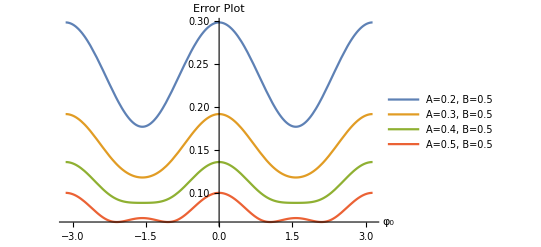

```mathematica
tempcheck1=Plot[{0.35355339059327373 √(-0.04000000000000001 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.12000000000000002 Sin[φ]^2)),0.23570226039551584 √(-0.09 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.27 Sin[φ]^2)),0.17677669529663687 √(-0.16000000000000003 Cos[φ]^4+0.25 Sin[φ]^2+Cos[φ]^2 (0.75-0.4800000000000001 Sin[φ]^2)),0.1414213562373095 √(0.4999999999999999 Cos[φ]^4+0.25 Sin[φ]^2)}, {φ, -Pi, Pi},AxesLabel->{Subscript[φ, 0],Style["Error Plot",FontWeight->Bold,Larger]},PlotLegends->{Style["A=0.2, B=0.5",Smaller],Style["A=0.3, B=0.5",Smaller],Style["A=0.4, B=0.5",Smaller],Style["A=0.5, B=0.5",Smaller]}]
```

```mathematica
ERROR=√((d2^2 (x0-x1)^2+d1^2 (x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

```mathematica
√((((1-x2)*x2)/100* (x0-x1)^2+((1-x1)*x1)/100* (x0-x2)^2+((1-x0)*x0)/100* (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

```mathematica
d2^2=((1-x2)*x2)/100
```

```mathematica
d1^2=((1-x1)*x1)/100
```

```mathematica
d0^2=((1-x0)*x0)/100
```

```mathematica
√((((1-x2)*x2)/100* (x0-x1)^2+((1-x1)*x1)/100* (x0-x2)^2+((1-x0)*x0)/100* (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

√((1/100 (1-x1) x1 (x0-x2)^2+1/100 (1-x0) x0 (x1-x2)^2+1/100 (x0-x1)^2 (1-x2) x2)/(x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2)

```mathematica
Simplify[√((1/100 (1-x1) x1 (x0-x2)^2+1/100 (1-x0) x0 (x1-x2)^2+1/100 (x0-x1)^2 (1-x2) x2)/(x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2)]
```

1/10 √((x1 x2 (x1+x2-2 x1 x2)+x0^2 (x1-2 x1^2+x2+2 x1 x2-2 x2^2)+x0 (2 x1 (-3+x2) x2+x2^2+x1^2 (1+2 x2)))/(x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2)

```mathematica
x0=((1+Cos[w*t])*Exp[-t/T])/2
```

```mathematica
x1=((1-Sin[w*t])*Exp[-t/T])/2
```

```mathematica
x2=((1-Cos[w*t])*Exp[-t/T])/2
```

```mathematica
√((1/100 (1-((1-Sin[w*t])*Exp[-t/T])/2)*((1-Sin[w*t])*Exp[-t/T])/2*(((1+Cos[w*t])*Exp[-t/T])/2-((1-Cos[w*t])*Exp[-t/T])/2)^2+1/100 (1-((1+Cos[w*t])*Exp[-t/T])/2) *((1+Cos[w*t])*Exp[-t/T])/2* (((1-Sin[w*t])*Exp[-t/T])/2-((1-Cos[w*t])*Exp[-t/T])/2)^2+1/100 (((1+Cos[w*t])*Exp[-t/T])/2-((1-Sin[w*t])*Exp[-t/T])/2)^2 (1-((1-Cos[w*t])*Exp[-t/T])/2) *((1-Cos[w*t])*Exp[-t/T])/2)/((((1+Cos[w*t])*Exp[-t/T])/2)^2-2*((1+Cos[w*t])*Exp[-t/T])/2*((1-Sin[w*t])*Exp[-t/T])/2+2 *(((1-Sin[w*t])*Exp[-t/T])/2)^2-2*((1-Sin[w*t])*Exp[-t/T])/2*((1-Cos[w*t])*Exp[-t/T])/2+(((1-Cos[w*t])*Exp[-t/T])/2)^2)^2)
```

√((1/200 ⅇ^(-t/T) (1-1/2 ⅇ^(-t/T) (1-Cos[t w])) (1-Cos[t w]) (1/2 ⅇ^(-t/T) (1+Cos[t w])-1/2 ⅇ^(-t/T) (1-Sin[t w]))^2+1/200 ⅇ^(-t/T) (1+Cos[t w]) (1-1/2 ⅇ^(-t/T) (1+Cos[t w])) (-1/2 ⅇ^(-t/T) (1-Cos[t w])+1/2 ⅇ^(-t/T) (1-Sin[t w]))^2+1/200 ⅇ^(-t/T) (-1/2 ⅇ^(-t/T) (1-Cos[t w])+1/2 ⅇ^(-t/T) (1+Cos[t w]))^2 (1-1/2 ⅇ^(-t/T) (1-Sin[t w])) (1-Sin[t w]))/(1/4 ⅇ^(-(2 t)/T) (1-Cos[t w])^2+1/4 ⅇ^(-(2 t)/T) (1+Cos[t w])^2-1/2 ⅇ^(-(2 t)/T) (1-Cos[t w]) (1-Sin[t w])-1/2 ⅇ^(-(2 t)/T) (1+Cos[t w]) (1-Sin[t w])+1/2 ⅇ^(-(2 t)/T) (1-Sin[t w])^2)^2)

```mathematica
Simplify[%5]
```

1/(20 √2)(√(-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w]))

```mathematica
Manipulate[Plot[1/(20 √2)(√(-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w])),{t,1,50}],{T,1,50},{w,12,30}]
```

```mathematica
1/(20 √2*(t^2))(√(-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w]))
```

1/(20 √2 t^2)(√(-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w]))

```mathematica
Manipulate[Plot[1/(20 √2 t^2)*(√(-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w])),{t,1,1000}],{T,1,300},{w,0.01,30}]
```

```mathematica
ERROR=√((d2^2 (x0-x1)^2+d1^2 (x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))
```

√((d2^2 (x0-x1)^2+d1^2 (x0-x2)^2+d0^2 (x1-x2)^2)/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
d0=√(((x0)*(1-x0))/(n*(Tall/(3*t))))
```

```mathematica
d1=√(((x1)*(1-x1))/(n*(Tall/(3*t))))
```

```mathematica
d2=√(((x2)*(1-x2))/(n*(Tall/(3*t))))
```

```mathematica
√((((x2)*(1-x2))/(n*(Tall/(3*t)))* (x0-x1)^2+((x1)*(1-x1))/(n*(Tall/(3*t)))* (x0-x2)^2+((x0)*(1-x0))/(n*(Tall/(3*t)))* (x1-x2)^2)/(x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2)
```

√(((3 t (1-x1) x1 (x0-x2)^2)/(n Tall)+(3 t (1-x0) x0 (x1-x2)^2)/(n Tall)+(3 t (x0-x1)^2 (1-x2) x2)/(n Tall))/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
Simplify[√(((3 t (1-x1) x1 (x0-x2)^2)/(n Tall)+(3 t (1-x0) x0 (x1-x2)^2)/(n Tall)+(3 t (x0-x1)^2 (1-x2) x2)/(n Tall))/((x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))]
```

√3 √((t (x1 x2 (x1+x2-2 x1 x2)+x0^2 (x1-2 x1^2+x2+2 x1 x2-2 x2^2)+x0 (2 x1 (-3+x2) x2+x2^2+x1^2 (1+2 x2))))/(n Tall (x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2))

```mathematica
x0=(((1+Cos[w*t])*Exp[-t/T])/2)
```

```mathematica
x1=(((1-Sin[w*t])*Exp[-t/T])/2)
```

```mathematica
x2=(((1-Cos[w*t])*Exp[-t/T])/2)
```

```mathematica
√3 √((t ((((1-Sin[w*t])*Exp[-t/T])/2)*(((1-Cos[w*t])*Exp[-t/T])/2)((((1-Sin[w*t])*Exp[-t/T])/2)+(((1-Cos[w*t])*Exp[-t/T])/2)-2*(((1-Sin[w*t])*Exp[-t/T])/2)* (((1-Cos[w*t])*Exp[-t/T])/2))+(((1+Cos[w*t])*Exp[-t/T])/2)^2* ((((1-Sin[w*t])*Exp[-t/T])/2)-2 *(((1-Sin[w*t])*Exp[-t/T])/2)^2+(((1-Cos[w*t])*Exp[-t/T])/2)+2*(((1-Sin[w*t])*Exp[-t/T])/2)* (((1-Cos[w*t])*Exp[-t/T])/2)-2 *(((1-Cos[w*t])*Exp[-t/T])/2)^2)+(((1+Cos[w*t])*Exp[-t/T])/2)* (2 *(((1-Sin[w*t])*Exp[-t/T])/2)* (-3+(((1-Cos[w*t])*Exp[-t/T])/2)) *(((1-Cos[w*t])*Exp[-t/T])/2)+(((1-Cos[w*t])*Exp[-t/T])/2)^2+(((1-Sin[w*t])*Exp[-t/T])/2)^2*(1+2 *(((1-Cos[w*t])*Exp[-t/T])/2)))))/(n Tall ((((1+Cos[w*t])*Exp[-t/T])/2)^2-2*(((1+Cos[w*t])*Exp[-t/T])/2)*(((1-Sin[w*t])*Exp[-t/T])/2)+2 *(((1-Sin[w*t])*Exp[-t/T])/2)^2-2 *(((1-Sin[w*t])*Exp[-t/T])/2)* (((1-Cos[w*t])*Exp[-t/T])/2)+(((1-Cos[w*t])*Exp[-t/T])/2)^2)^2))
```

√3 √((t (1/4 ⅇ^(-(2 t)/T) (1+Cos[t w])^2 (1/2 ⅇ^(-t/T) (1-Cos[t w])-1/2 ⅇ^(-(2 t)/T) (1-Cos[t w])^2+1/2 ⅇ^(-t/T) (1-Sin[t w])+1/2 ⅇ^(-(2 t)/T) (1-Cos[t w]) (1-Sin[t w])-1/2 ⅇ^(-(2 t)/T) (1-Sin[t w])^2)+1/2 ⅇ^(-t/T) (1+Cos[t w]) (1/4 ⅇ^(-(2 t)/T) (1-Cos[t w])^2+1/2 ⅇ^(-(2 t)/T) (-3+1/2 ⅇ^(-t/T) (1-Cos[t w])) (1-Cos[t w]) (1-Sin[t w])+1/4 ⅇ^(-(2 t)/T) (1+ⅇ^(-t/T) (1-Cos[t w])) (1-Sin[t w])^2)+1/4 ⅇ^(-(2 t)/T) (1-Cos[t w]) (1/2 ⅇ^(-t/T) (1-Cos[t w])+1/2 ⅇ^(-t/T) (1-Sin[t w])-1/2 ⅇ^(-(2 t)/T) (1-Cos[t w]) (1-Sin[t w])) (1-Sin[t w])))/(n Tall (1/4 ⅇ^(-(2 t)/T) (1-Cos[t w])^2+1/4 ⅇ^(-(2 t)/T) (1+Cos[t w])^2-1/2 ⅇ^(-(2 t)/T) (1-Cos[t w]) (1-Sin[t w])-1/2 ⅇ^(-(2 t)/T) (1+Cos[t w]) (1-Sin[t w])+1/2 ⅇ^(-(2 t)/T) (1-Sin[t w])^2)^2))

```mathematica
Tall=500
n=100
```

500

100

```mathematica
Simplify[%24]
```

```mathematica
1/2 √(3/2) √(1/(n Tall)t (-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w]))
```

1/2 √(3/2) √(1/(n Tall)t (-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w]))

```mathematica
Manipulate[Plot[1/(2*t^2) √(3/2) √(1/(n Tall)t (-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w]+Cos[4 t w]+8 Sin[t w]-8 ⅇ^(t/T) Sin[t w]+8 Sin[3 t w]-8 ⅇ^(t/T) Sin[3 t w])),{t,0,150}],{n,100,1000},{T,20,50},{Tall,500,5000},{w,0.01,30}]
```

```mathematica
Abs[Subscript[δω, 0]]==√((1-cos^2(Δt)e^(-2γt))/(nTt e^(-2γt)sin^2(Δt)))
```

```mathematica
√((1-(Cos[w*t])^2*Exp[-2*t/T])/(n*Tall*t*Exp[-2*t/T]*Sin[w*t]^2))
```

√((ⅇ^((2 t)/T) (1-ⅇ^(-(2 t)/T) Cos[t w]^2) Csc[t w]^2)/(n t Tall))

```mathematica
Manipulate[Plot[√((ⅇ^((2 t)/T) (1-ⅇ^(-(2 t)/T) Cos[t w]^2) Csc[t w]^2)/(n t Tall)),{t,0,50}],{n,100,1000},{T,20,50},{Tall,500,5000},{w,0.01,30}]
```

```mathematica
T=10
```

10

```mathematica
n=100
```

100

```mathematica
Tall=500
```

500

```mathematica
w=0.001
```

0.001

```mathematica
FindMinimum[Abs[√((ⅇ^((2 t)/T) (1-ⅇ^(-(2 t)/T) Cos[t w]^2) Csc[t w]^2)/(n t Tall))],{t,14}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.335516,{t→14.1065}}

```mathematica
√(1/(n *14.106509527647479*Tall)ⅇ^((2 *14.106509527647479)/T) (1-ⅇ^(-(2  *14.106509527647479)/T) Cos[14.106509527647479* w]^2) Csc[14.106509527647479* w]^2)
```

0.335516

```mathematica
T=10
```

10

```mathematica
n=100
```

100

```mathematica
Tall=500
```

500

```mathematica
w=30
```

30

```mathematica
√(1/(n *4.764757751632404*Tall)ⅇ^((2*4.764757751632404)/T) (1-ⅇ^(-(2*4.764757751632404)/T) Cos[4.764757751632404* w]^2) Csc[4.764757751632404* w]^2)
```

0.00329933

```mathematica
√((2*E)/(n*Tall*T))
```

(√ⅇ)/500

```mathematica
N[(√ⅇ)/500]
```

0.00329744

```mathematica
phase = ArcCos[(2*P-1)*Exp[t/T]]
```

```mathematica
T=10
```

10

```mathematica
n=100
```

100

```mathematica
Tall=500
```

500

```mathematica
w=0.1
```

0.1

```mathematica
FindMinimum[Abs[√((ⅇ^((2 t)/T) (1-ⅇ^(-(2 t)/T) Cos[t w]^2) Csc[t w]^2)/(n t Tall))],{t,5}]
```

{0.00447525,{t→10.2502}}

```mathematica
√(1/(n *10.250242304054334*Tall)ⅇ^((2 *10.250242304054334)/T) (1-ⅇ^(-(2 *10.250242304054334)/T) Cos[10.250242304054334*w]^2) Csc[10.250242304054334* w]^2)
```

0.00447525

```mathematica
Manipulate[Plot[1/(2*t^2) √(3/2) √(1/(n Tall)t (-11+16 ⅇ^(t/T)+(-6+8 ⅇ^(t/T)) Cos[2 t w+Pi/1]+Cos[4 (w*t+Pi/2)]+8 Sin[t w+Pi/2]-8 ⅇ^(t/T) Sin[w*t+Pi/2]+8 Sin[3 (t w+Pi/2)]-8 ⅇ^(t/T) Sin[3( t w+Pi/2)])),{t,0,150}],{n,100,1000},{T,20,50},{Tall,500,5000},{w,0.0000001,30}]
```

```mathematica
1/10 √((x1 x2 (x1+x2-2 x1 x2)+x0^2 (x1-2 x1^2+x2+2 x1 x2-2 x2^2)+x0 (2 x1 (-3+x2) x2+x2^2+x1^2 (1+2 x2)))/(x0^2-2 x0 x1+2 x1^2-2 x1 x2+x2^2)^2)
```

```mathematica
x0=(1+Cos[w*t]*Exp[-t/T])/2
```

```mathematica
x1=(1-Sin[w*t]*Exp[-t/T])/2
```

```mathematica
x2=(1-Cos[w*t]*Exp[-t/T])/2
```

```mathematica
1/10 √(((1-Sin[w*t]*Exp[-t/T])/2*(1-Cos[w*t]*Exp[-t/T])/2((1-Sin[w*t]*Exp[-t/T])/2+(1-Cos[w*t]*Exp[-t/T])/2-2 *(1-Sin[w*t]*Exp[-t/T])/2*(1-Cos[w*t]*Exp[-t/T])/2)+((1+Cos[w*t]*Exp[-t/T])/2)^2 ((1-Sin[w*t]*Exp[-t/T])/2-2 *((1-Sin[w*t]*Exp[-t/T])/2)^2+(1-Cos[w*t]*Exp[-t/T])/2+2 *(1-Sin[w*t]*Exp[-t/T])/2*(1-Cos[w*t]*Exp[-t/T])/2-2 *((1-Cos[w*t]*Exp[-t/T])/2)^2)+(1+Cos[w*t]*Exp[-t/T])/2* (2*(1-Sin[w*t]*Exp[-t/T])/2* (-3+(1-Cos[w*t]*Exp[-t/T])/2)*(1-Cos[w*t]*Exp[-t/T])/2+((1-Cos[w*t]*Exp[-t/T])/2)^2+((1-Sin[w*t]*Exp[-t/T])/2)^2*(1+2 *(1-Cos[w*t]*Exp[-t/T])/2)))/(((1+Cos[w*t]*Exp[-t/T])/2)^2-2 *(1+Cos[w*t]*Exp[-t/T])/2* (1-Sin[w*t]*Exp[-t/T])/2+2 *((1-Sin[w*t]*Exp[-t/T])/2)^2-2*(1-Sin[w*t]*Exp[-t/T])/2* (1-Cos[w*t]*Exp[-t/T])/2+((1-Cos[w*t]*Exp[-t/T])/2)^2)^2)
```

1/10 √((1/4 (1-ⅇ^(-t/10) Cos[0.1 t]) (1-ⅇ^(-t/10) Sin[0.1 t]) (1/2 (1-ⅇ^(-t/10) Cos[0.1 t])+1/2 (1-ⅇ^(-t/10) Sin[0.1 t])-1/2 (1-ⅇ^(-t/10) Cos[0.1 t]) (1-ⅇ^(-t/10) Sin[0.1 t]))+1/4 (1+ⅇ^(-t/10) Cos[0.1 t])^2 (1/2 (1-ⅇ^(-t/10) Cos[0.1 t])-1/2 (1-ⅇ^(-t/10) Cos[0.1 t])^2+1/2 (1-ⅇ^(-t/10) Sin[0.1 t])+1/2 (1-ⅇ^(-t/10) Cos[0.1 t]) (1-ⅇ^(-t/10) Sin[0.1 t])-1/2 (1-ⅇ^(-t/10) Sin[0.1 t])^2)+1/2 (1+ⅇ^(-t/10) Cos[0.1 t]) (1/4 (1-ⅇ^(-t/10) Cos[0.1 t])^2+1/2 (1-ⅇ^(-t/10) Cos[0.1 t]) (-3+1/2 (1-ⅇ^(-t/10) Cos[0.1 t])) (1-ⅇ^(-t/10) Sin[0.1 t])+1/4 (2-ⅇ^(-t/10) Cos[0.1 t]) (1-ⅇ^(-t/10) Sin[0.1 t])^2))/(1/4 (1-ⅇ^(-t/10) Cos[0.1 t])^2+1/4 (1+ⅇ^(-t/10) Cos[0.1 t])^2-1/2 (1-ⅇ^(-t/10) Cos[0.1 t]) (1-ⅇ^(-t/10) Sin[0.1 t])-1/2 (1+ⅇ^(-t/10) Cos[0.1 t]) (1-ⅇ^(-t/10) Sin[0.1 t])+1/2 (1-ⅇ^(-t/10) Sin[0.1 t])^2)^2)

```mathematica
Simplify[%75]
```

1/20 √(6 ⅇ^(t/5) Cos[0.1 t]^2-2 Cos[0.1 t]^4+2 ⅇ^(t/5) Sin[0.1 t]^2-3/2 Sin[0.2 t]^2)

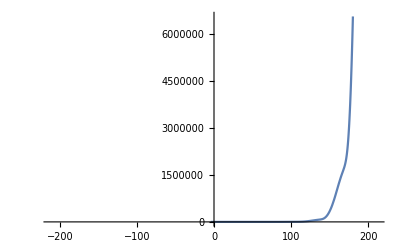

```mathematica
Plot[1/20 √(6 ⅇ^(t/5) Cos[0.1 t]^2-2 Cos[0.1 t]^4+2 ⅇ^(t/5) Sin[0.1 t]^2-3/2 Sin[0.2 t]^2),{t,-212.05750411731103,212.05750411731103}]
```